Grid

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
pts={};
nPts=11;
Do[
Do[
AppendTo[pts,{(i-1)/10.0,(j-1)/10.0}];
,{j,1,nPts}];
,{i,1,nPts}];
```

```mathematica
f=OpenWrite["grid.txt"];
Do[
s=ToString[pt[[1]]]<>" "<>ToString[pt[[2]]];
WriteLine[f,s];
,{pt,pts}];
Close[f];
```

Data

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data={};
radius=0.3;
nData=100;
Do[
x=0.5+radius*Cos[2*Pi*(i-1)/(nData-1)];
y=0.5+radius*Sin[2*Pi*(i-1)/(nData-1)];
If[i≠nData,
z=Abs[i-0.5*nData]/(0.5*nData),
z=data[[1,3]]
];
AppendTo[data,{x,y,z}];
,{i,1,nData}];
```

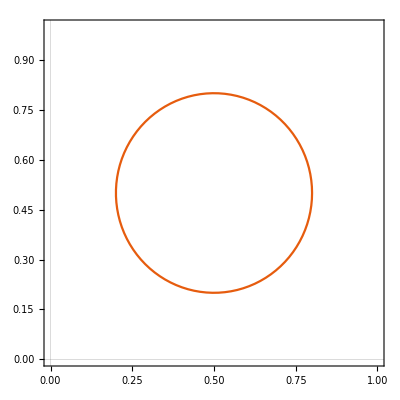

```mathematica
ListLinePlot[data[[;;,{1,2}]],AspectRatio->1,PlotRange->{{0,1},{0,1}}]
```

```mathematica
Show[
ListPointPlot3D[data,PlotRange->{{0,1},{0,1},{0,1}}],
ListPointPlot3D[data,PlotRange->{{0,1},{0,1},{0,1}}]/.Point->Line
]
```

-Graphics3D-

```mathematica
f=OpenWrite["path.txt"];
Do[
s=ToString[pt[[1]]]<>" "<>ToString[pt[[2]]]<>" "<>ToString[pt[[3]]];
WriteLine[f,s];
,{pt,data}];
Close[f];
```

Test

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
dataPath=Import["path.txt","Table"];
```

```mathematica
pltPath=Show[
ListPointPlot3D[dataPath,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Black],
ListPointPlot3D[dataPath,PlotRange->{{0,1},{0,1},{0,1}},PlotStyle->Black]/.Point->Line
]
```

-Graphics3D-

```mathematica
dataSol=Import["solution.txt","Table"];
```

```mathematica
Show[ListPointPlot3D[dataSol,PlotStyle->Red,PlotRange->{{-0.05,1.05},{-0.05,1.05},{-2,2}}],pltPath]
```

-Graphics3D-

Test interpolate a data point

### Funcs

```mathematica
coeffs[p0_,p1_,p2_,p3_,x_]:=Module[
{a}
,
a=Association[];
a["0"]=-1/2*x^3+x^2-1/2*x;
a["1"]=3/2*x^3-5/2*x^2+1;
a["2"]=-3/2*x^3+2*x^2+1/2*x;
a["3"]=1/2*x^3-1/2*x^2;

Return[a];
];
```

```mathematica
fInterp[p0_,p1_,p2_,p3_,x_]:=Module[
{a}
,
a=coeffs[p0,p1,p2,p3,x];
Return[p0*a["0"]+p1*a["1"]+p2*a["2"]+p3*a["3"]];
];
```

### Test interp 1d

```mathematica
fakeData=Table[{(i-1)/20//N,RandomReal[{0,1}]},{i,21}];
```

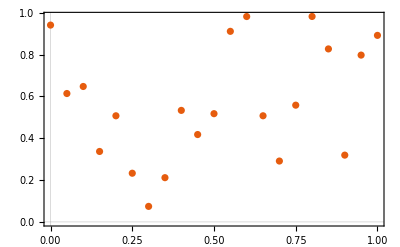

```mathematica
ListPlot[fakeData]
```

```mathematica
fakeData
```

{{0.,0.940654},{0.05,0.61358},{0.1,0.647235},{0.15,0.336627},{0.2,0.507152},{0.25,0.232643},{0.3,0.0741308},{0.35,0.211363},{0.4,0.532948},{0.45,0.417563},{0.5,0.51726},{0.55,0.910803},{0.6,0.98156},{0.65,0.507203},{0.7,0.290885},{0.75,0.55789},{0.8,0.981892},{0.85,0.826762},{0.9,0.319135},{0.95,0.797211},{1.,0.891488}}

### Try 2 pts compare

```mathematica
pt1=0.33;
pt2=0.36;
```

```mathematica
delta=0.05;
pt1nbr4=Select[fakeData,Abs[#[[1]]-pt1]≤2*delta&];
pt2nbr4=Select[fakeData,Abs[#[[1]]-pt2]≤2*delta&];
```

```mathematica
fInterp[pt1nbr4[[1,2]],pt1nbr4[[2,2]],pt1nbr4[[3,2]],pt1nbr4[[4,2]],0]
```

0.0741308

```mathematica
pt1nbr4[[2,2]]
```

0.0741308

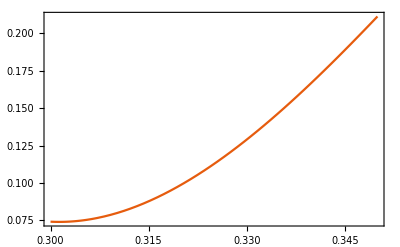

```mathematica
plt1=Plot[fInterp[pt1nbr4[[1,2]],pt1nbr4[[2,2]],pt1nbr4[[3,2]],pt1nbr4[[4,2]],(x-0.3)/delta],{x,0.3,0.3+delta}]
```

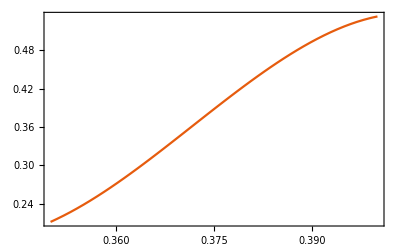

```mathematica
plt2=Plot[fInterp[pt2nbr4[[1,2]],pt2nbr4[[2,2]],pt2nbr4[[3,2]],pt2nbr4[[4,2]],(x-0.35)/delta],{x,0.35,0.35+delta}]
```

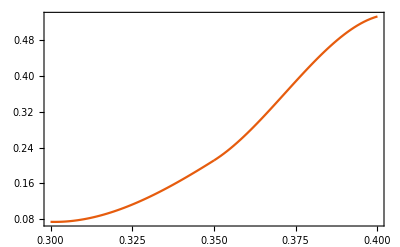

```mathematica
Show[plt1,plt2,PlotRange->All]
```

### Try domain

```mathematica
gridEval=Table[x,{x,0.06,0.94,0.01}];
```

```mathematica
gridInterp={};
Do[
nbr4=Select[fakeData,Abs[#[[1]]-gridPt]≤2*delta&];
yInterp=fInterp[nbr4[[1,2]],nbr4[[2,2]],nbr4[[3,2]],nbr4[[4,2]],(gridPt-nbr4[[2,1]])/(nbr4[[3,1]]-nbr4[[2,1]])];
AppendTo[gridInterp,{gridPt,yInterp}];
,{gridPt,gridEval}];
```

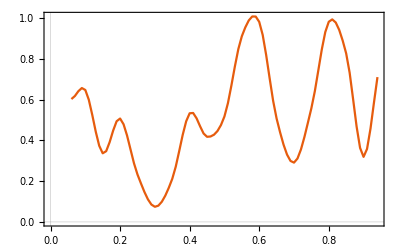

```mathematica
ListLinePlot[gridInterp]
```

```mathematica
fInterp2[x_,y_]:=Module[
{find,delta,nbr4,xUnique,lines,qs,zInterp}
,
(* Try to find *)
find=Select[dataSol,#[[1]]==x&&#[[2]]==y&];
If[find≠{},Return[find[[1,3]]]];

(* Interpolate *)
delta=0.05;
nbr4=Select[dataSol,Abs[#[[1]]-x]≤2*delta&&Abs[#[[2]]-y]≤2*delta&];
xUnique=Sort[DeleteDuplicates[nbr4[[;;,1]]]];
lines=Table[Select[nbr4,#[[1]]==xUnique[[iLine]]&],{iLine,1,4}];
qs=Table[fInterp[lines[[iLine,1,3]],lines[[iLine,2,3]],lines[[iLine,3,3]],lines[[iLine,4,3]],(y-lines[[iLine,2,2]])/(lines[[iLine,3,2]]-lines[[iLine,2,2]])],{iLine,1,4}];
zInterp=fInterp[qs[[1]],qs[[2]],qs[[3]],qs[[4]],(x-xUnique[[2]])/(xUnique[[3]]-xUnique[[2]])];
Return[zInterp]
];
```

```mathematica
{x,y,z}=dataPath[[3]]
```

{0.797586,0.537978,0.94}

```mathematica
fInterp2[x,y]
```

0.94

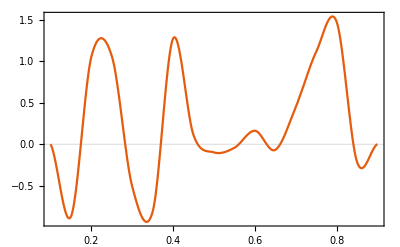

```mathematica
Plot[fInterp2[x,0.3],{x,2*delta,1-2*delta}]
```

Interp a bunch of values

```mathematica
gridInterp=Flatten[Table[{i,j},{i,delta+0.01,1-delta-0.01,0.01},{j,delta+0.01,1-delta-0.01,0.01}],1];
```

```mathematica
dataInterp={};
Do[
AppendTo[dataInterp,{d[[1]],d[[2]],fInterp2[d[[1]],d[[2]]]}]
,{d,gridInterp}];
```

```mathematica
pltInterp=ListPointPlot3D[dataInterp]
```

-Graphics3D-

```mathematica
Show[pltInterp,pltPath]
```

-Graphics3D-

Compare values along the path

```mathematica
pathTest={};
radius=0.3;
nData=1000;
Do[
x=0.5+radius*Cos[2*Pi*(i-1)/(nData-1)];
y=0.5+radius*Sin[2*Pi*(i-1)/(nData-1)];
AppendTo[pathTest,{x,y}];
,{i,1,nData}];
```

```mathematica
pathInterp={};
Do[
AppendTo[pathInterp,{d[[1]],d[[2]],fInterp2[d[[1]],d[[2]]]}]
,{d,pathTest}];
```

```mathematica
Show[ListPointPlot3D[pathInterp]]
```

-Graphics3D-

Interp using mathematica

```mathematica
cubic=Interpolation[dataSol,InterpolationOrder->3]
```

InterpolatingFunction[…]

```mathematica
cubic[x,y]
```

2.65086

```mathematica
Show[Plot3D[cubic[x,y],{x,0,1},{y,0,1},Mesh->False,PlotRange->{{-0.05,1.05},{-0.05,1.05},{-0.05,1}}],pltPath]
```

-Graphics3D-